# Ques_03: Equations.

Let

```mathematica
f[x_]:=(x^3-5 x^2+3x+1)/(2 x^2+x-1);          h[x_]:=Sin[x/3] - Cos[x^3/5]
```

1. Find the three exact solutions of f(x)=0.

```mathematica
Solve[f[x]==0]
```

{{x→1},{x→2-√5},{x→2+√5}}

other way

```mathematica
Solve[(x^3-5 x^2+3x+1)/(2 x^2+x-1)==0]
```

{{x→1},{x→2-√5},{x→2+√5}}

```mathematica
N[%]
```

{{x→1.},{x→-0.236068},{x→4.23607}}

The three solutions arranged from small to large are:
x_1=  2-√5   ,x_2=    1        ,x_3=     2+√5

2 .	Find  x ∈ ℝ such as  f(x) ≥0

```mathematica
Reduce[(x^3-5 x^2+3x+1)/(2 x^2+x-1)≥0,x]
```

-1<x≤2-√5||1/2<x≤1||x≥2+√5

Other harder way for solving the same exercise:

```mathematica
Solve[2 x^2+x-1==0]
```

{{x→-1},{x→1/2}}

The points where the function may change the sign are {{x→1},{x→2-√5},{x→2+√5}} and {{x→-1},{x→1/2}} . We can arrange the points  in increasing orderto see the intervals easily {x→-1},{x→2-√5},{x→1/2},{x→1},x→2+√5}, so

```mathematica
(x^3-5 x^2+3x+1)/(2 x^2+x-1)/. x->{-500,-0.8,0,0.75,0.3,500}
```

{-11477409/45409,9.83077,-1,0.982143,-2.84038,123751501/500499}

The solution is:
]  -1    , 2-√5    ]     ∪     ]  1/2      ,1  ]   ∪     [  2+√5      ,+∞[

we can verify the above solution using  Plot[]

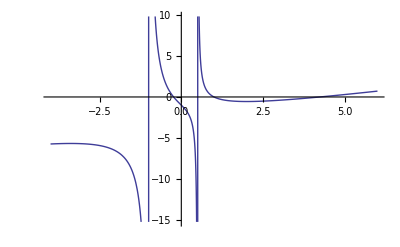

```mathematica
Plot[(x^3-5 x^2+3x+1)/(2 x^2+x-1),{x,-4,6}]
```

3.	Obtain the approximated value of the point where the minimum of h(x) is reached near x=3

```mathematica
D[Sin[x/3] - Cos[x^3/5],x]
```

1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]

Solve and NSolve is not going to give us a solution of the problem

```mathematica
Solve[%==0,x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]

```mathematica
NSolve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]
```

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

NSolve[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5]==0,x]

So that we need to use FindRoot

```mathematica
FindRoot[1/3 Cos[x/3]+3/5 x^2 Sin[x^3/5], {x, 3.}]
```

{x→3.1507}

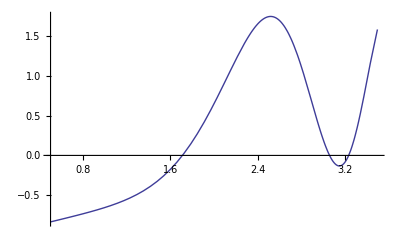

```mathematica
Plot[Sin[x/3] - Cos[x^3/5],{x,0.5,3.5}]
```

m≈3.1507

you can use mouse position to check the solution

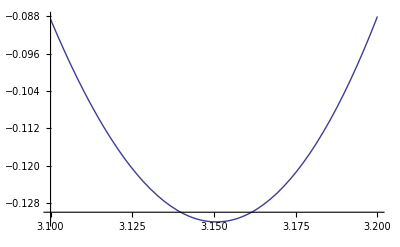

```mathematica
AA=Plot[Sin[x/3] - Cos[x^3/5],{x,3.1,3.2}]
```

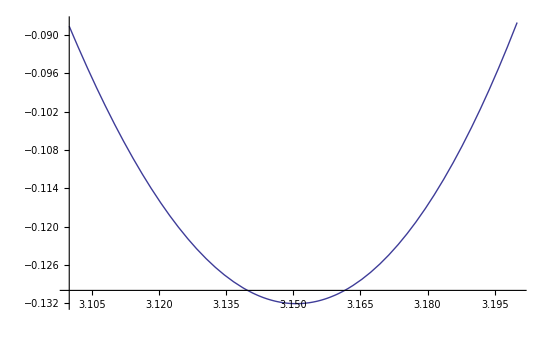

```mathematica
{Graphics[AA,ImageSize->100],Dynamic[MousePosition["Graphics","Mouse not in graphics!"]]}
```